```mathematica
Ejercicio. 5.1.
Considera la curva en R dada por las ecuaciones paramétricas:
x = sen(t), y = sen(2t),
donde t es el parámetro.

(1) Dibuja esta curva mediante la orden de Mathematica “ParametricPlot”.
```

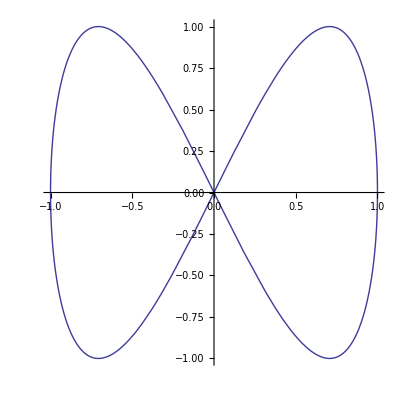

```mathematica
ParametricPlot[{Sin[u],Sin[2 u]},{u,0,2 Pi}]
```

```mathematica
(2) Determina la ecuación implícita que define esta curva.
```

```mathematica
Reduce[x-Sin[t]==0,t]
```

C[1]∈Integers&&(t==π-ArcSin[x]+2 π C[1]||t==ArcSin[x]+2 π C[1])

```mathematica
Reduce[y-Sin[2*t]==0,t]
```

C[1]∈Integers&&(t==1/2 (π-ArcSin[y]+2 π C[1])||t==1/2 (ArcSin[y]+2 π C[1]))

```mathematica
(3) Dibuja la curva, dada por la ecuación implícita, mediante la orden de Mathematica “ContourPlot”:

utilizamos la expresión de igualar ambos miembros anteriores, obteniendo la función a trozos:
```

Syntax::sntxf: "(3) Dibuja la curva" cannot be followed by ", dada por la ecuación implícita, mediante la orden de Mathematica
      “ContourPlot”".

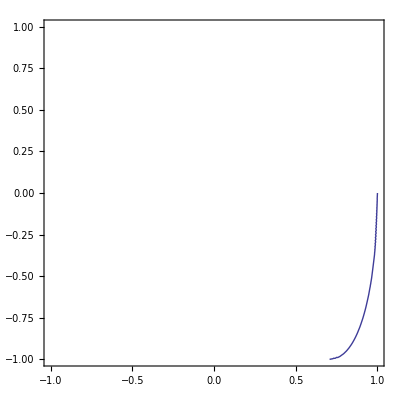

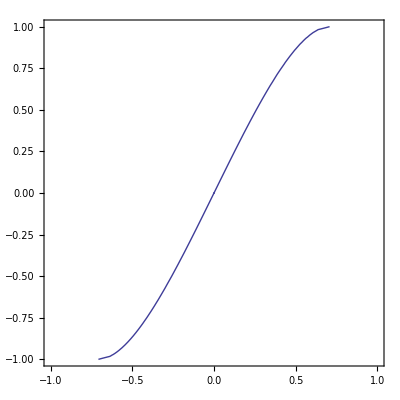

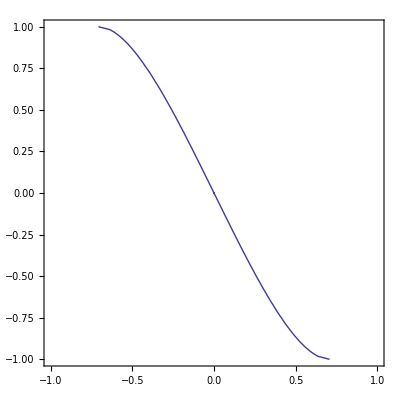

```mathematica
ContourPlot[ Pi-ArcSin[x]-(1/2*(Pi-ArcSin[y]))==0 ,{x,-1,1},{y,-1,1}]
ContourPlot[ (ArcSin[x]) -(  1/2 (ArcSin[y]))==0 ,{x,-1,1},{y,-1,1}]
ContourPlot[ -(ArcSin[x]) -(  1/2 (ArcSin[y]))==0 ,{x,-1,1},{y,-1,1}]
```